{{Version V1.1,Start Time: 15-03-2022_170507},{Time,Angle (deg)},{82606.7,-0.346246},{82606.7,-0.36946},861836,{84439.1,-0.320518},{84439.1,-0.320704},{84439.1,-0.332234}}
 |  |  |  |

Plot unsmoothed points

separate elements

Recombine original truncated data Elements

Plot original elements

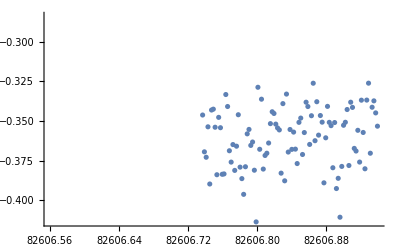

Process Gaussian Smoothing

Recombine Moving Average Elements

Process Bilateral Smoothing

Recombine Moving Average Elements

Process Moving Average Smoothing

Recombine Moving Average Elements

Part::partw: Part 92 of {-0.360324,-0.361124,-0.36254,-0.363591,-0.361555,-0.356668,-0.359237,-0.362575,«36»,-0.363725,-0.360522,-0.361433,-0.359773,-0.362199,-0.359056,«41»} does not exist.

Part::partw: Part 93 of {-0.360324,-0.361124,-0.36254,-0.363591,-0.361555,-0.356668,-0.359237,-0.362575,«36»,-0.363725,-0.360522,-0.361433,-0.359773,-0.362199,-0.359056,«41»} does not exist.

Part::partw: Part 94 of {-0.360324,-0.361124,-0.36254,-0.363591,-0.361555,-0.356668,-0.359237,-0.362575,«36»,-0.363725,-0.360522,-0.361433,-0.359773,-0.362199,-0.359056,«41»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot / Compare souce against all smoothed options

Part::partw: Part 92 of {-0.360324,-0.361124,-0.36254,-0.363591,-0.361555,-0.356668,-0.359237,-0.362575,«36»,-0.363725,-0.360522,-0.361433,-0.359773,-0.362199,-0.359056,«41»} does not exist.

Part::partw: Part 93 of {-0.360324,-0.361124,-0.36254,-0.363591,-0.361555,-0.356668,-0.359237,-0.362575,«36»,-0.363725,-0.360522,-0.361433,-0.359773,-0.362199,-0.359056,«41»} does not exist.

Part::partw: Part 94 of {-0.360324,-0.361124,-0.36254,-0.363591,-0.361555,-0.356668,-0.359237,-0.362575,«36»,-0.363725,-0.360522,-0.361433,-0.359773,-0.362199,-0.359056,«41»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

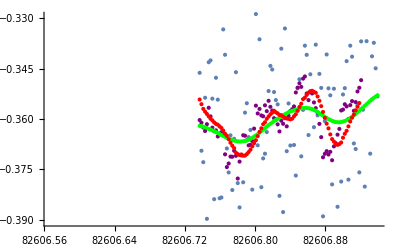

Perform Second BiLateral Smoothing of Original BiLateral Table

Recombine Moving Average Elements

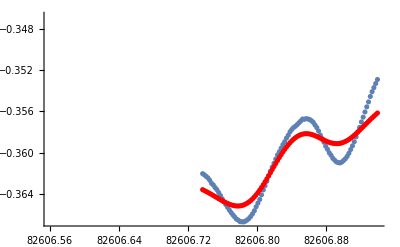

```mathematica
(*runData = Import["/Users/plentz/Documents/Parallax621Project/experiment/Results/2d/run2/SteadyState_15MAR22_505-535pm.csv", "CSV"]*)
runData = Import["/Users/plentz/Documents/Parallax621Project/experiment/Results/2d/run2/SteadyState_15MAR22_505-535pm.csv", "CSV"]
Print["Plot unsmoothed points"]
length = Length[runData] - 2;
length = 100;
angle= Table[i, {i,length}];
savedSmoothedAngle= Table[i, {i,length}];
time = Table[i, {i,length}];
Print["separate elements"]
For[i=1,i<length,i++,{
time[[i]] =runData[[i + 2, 1]];
angle[[i]] =runData[[i + 2, 2]];
}
]
originalTable = Table[i + j, {i,length}, {j, 2}];
Print["Recombine original truncated data Elements"]
For[i=1,i<length,i++,{
originalTable[[i,1]] =time[[i]];
originalTable[[i,2]] =angle[[i]];
}
]
Print["Plot original elements"]
ListPlot[originalTable]
Print["Process Gaussian Smoothing"]
filtered = GaussianFilter[angle,10];
recombinedGaussianTable = Table[i + j, {i,length}, {j, 2}];
Print["Recombine Moving Average Elements"]
For[i=1,i<length,i++,{
recombinedGaussianTable[[i,1]] =time[[i]];
recombinedGaussianTable[[i,2]] =filtered[[i]];
}
]
Print["Process Bilateral Smoothing"]
filtered = BilateralFilter[angle,10,1];
recombinedBiLateralTable = Table[i + j, {i,length}, {j, 2}];
Print["Recombine Moving Average Elements"]
For[i=1,i<length,i++,{
recombinedBiLateralTable[[i,1]] =time[[i]];
recombinedBiLateralTable[[i,2]] =filtered[[i]];
savedSmoothedAngle[[i]] = filtered[[i]];
}
]
Print["Process Moving Average Smoothing"]
filtered = MovingAverage[angle,10];
recombinedMovingAverageTable = Table[i + j, {i,length}, {j, 2}];
Print["Recombine Moving Average Elements"]
For[i=1,i<length,i++,{
recombinedMovingAverageTable[[i,1]] =time[[i]];
recombinedMovingAverageTable[[i,2]] =filtered[[i]];
}
]
Print["Plot / Compare souce against all smoothed options"]
ListPlot[{originalTable,recombinedMovingAverageTable, recombinedBiLateralTable, recombinedGaussianTable},PlotStyle->{Thin,Purple, Green, Red}]

(*            Second Iteration           *)
Print["Perform Second BiLateral Smoothing of Original BiLateral Table"]
filtered = BilateralFilter[savedSmoothedAngle,10,1];
recombinedSecondBiLateralTable = Table[i + j, {i,length}, {j, 2}];
Print["Recombine Moving Average Elements"]
For[i=1,i<length,i++,{
recombinedSecondBiLateralTable[[i,1]] =time[[i]];
recombinedSecondBiLateralTable[[i,2]] =filtered[[i]];
}
]
ListPlot[{recombinedBiLateralTable, recombinedSecondBiLateralTable},PlotStyle->{Thin, Red}]
```